{{p,L,n,Pfail,Prod,I},{0.01,3.,10.,0.0584726,0.584726,0.233588},{0.01,5.,34.,0.0049434,0.168076,0.020458},{0.01,7.,74.,0.0043856,0.324534,0.0368854},{0.01,9.,130.,0.0004316,0.056108,0.00519944},{0.01,11.,202.,0.0000671,0.0135542,0.000989499},{0.02,3.,10.,0.114347,1.14347,0.335684},{0.02,5.,34.,0.020639,0.701726,0.061015},{0.02,7.,74.,0.0177189,1.3112,0.109603},{0.02,9.,130.,0.0037178,0.483314,0.0324689},{0.02,11.,202.,0.0008404,0.169761,0.00975441},{0.03,3.,10.,0.166826,1.66826,0.386078},{0.03,5.,34.,0.0474813,1.61436,0.108745},{0.03,7.,74.,0.0420669,3.11295,0.232023},{0.03,9.,130.,0.0132858,1.72715,0.0985687},{0.03,11.,202.,0.0043919,0.887164,0.0406386},{0.04,3.,10.,0.217011,2.17011,0.40928},{0.04,5.,34.,0.0844252,2.87046,0.154669},{0.04,7.,74.,0.0727297,5.382,0.286019},{0.04,9.,130.,0.0331808,4.3135,0.20565},{0.04,11.,202.,0.0150664,3.04341,0.112697},{0.05,3.,10.,0.264802,2.64802,0.413209},{0.05,5.,34.,0.129787,4.41276,0.193342},{0.05,7.,74.,0.115548,8.55055,0.264034},{0.05,9.,130.,0.0673807,8.75949,0.351354},{0.05,11.,202.,0.0396381,8.0069,0.240566}}

{p,L,n,Pfail,Prod,I}

{{0.01,3.,10.,0.0584726,0.584726,0.233588},{0.01,5.,34.,0.0049434,0.168076,0.020458},{0.01,7.,74.,0.0043856,0.324534,0.0368854},{0.01,9.,130.,0.0004316,0.056108,0.00519944},{0.01,11.,202.,0.0000671,0.0135542,0.000989499},{0.02,3.,10.,0.114347,1.14347,0.335684},{0.02,5.,34.,0.020639,0.701726,0.061015},{0.02,7.,74.,0.0177189,1.3112,0.109603},{0.02,9.,130.,0.0037178,0.483314,0.0324689},{0.02,11.,202.,0.0008404,0.169761,0.00975441},{0.03,3.,10.,0.166826,1.66826,0.386078},{0.03,5.,34.,0.0474813,1.61436,0.108745},{0.03,7.,74.,0.0420669,3.11295,0.232023},{0.03,9.,130.,0.0132858,1.72715,0.0985687},{0.03,11.,202.,0.0043919,0.887164,0.0406386},{0.04,3.,10.,0.217011,2.17011,0.40928},{0.04,5.,34.,0.0844252,2.87046,0.154669},{0.04,7.,74.,0.0727297,5.382,0.286019},{0.04,9.,130.,0.0331808,4.3135,0.20565},{0.04,11.,202.,0.0150664,3.04341,0.112697},{0.05,3.,10.,0.264802,2.64802,0.413209},{0.05,5.,34.,0.129787,4.41276,0.193342},{0.05,7.,74.,0.115548,8.55055,0.264034},{0.05,9.,130.,0.0673807,8.75949,0.351354},{0.05,11.,202.,0.0396381,8.0069,0.240566}}

{{{3.,0.584726},{5.,0.168076},{7.,0.324534},{9.,0.056108},{11.,0.0135542}},{{3.,1.14347},{5.,0.701726},{7.,1.3112},{9.,0.483314},{11.,0.169761}},{{3.,1.66826},{5.,1.61436},{7.,3.11295},{9.,1.72715},{11.,0.887164}},{{3.,2.17011},{5.,2.87046},{7.,5.382},{9.,4.3135},{11.,3.04341}},{{3.,2.64802},{5.,4.41276},{7.,8.55055},{9.,8.75949},{11.,8.0069}}}

{{{3.,0.233588},{5.,0.020458},{7.,0.0368854},{9.,0.00519944},{11.,0.000989499}},{{3.,0.335684},{5.,0.061015},{7.,0.109603},{9.,0.0324689},{11.,0.00975441}},{{3.,0.386078},{5.,0.108745},{7.,0.232023},{9.,0.0985687},{11.,0.0406386}},{{3.,0.40928},{5.,0.154669},{7.,0.286019},{9.,0.20565},{11.,0.112697}},{{3.,0.413209},{5.,0.193342},{7.,0.264034},{9.,0.351354},{11.,0.240566}}}

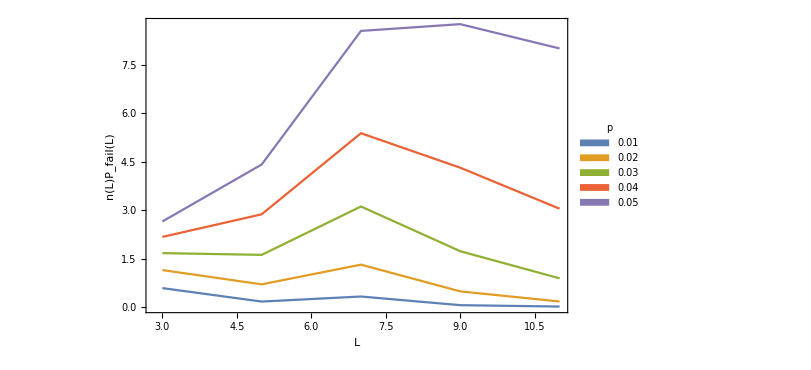

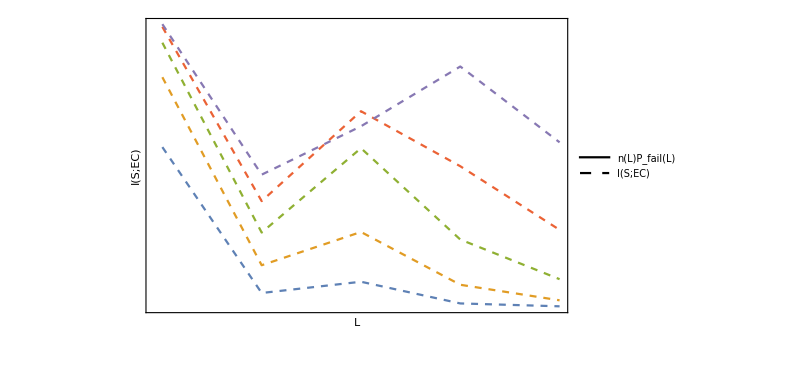

w3.pdf

```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["w3_results.xlsx"][[1]]
sNames=s[[1]]
sData=s[[2;;]]
DataPlotProd=Partition[Transpose[{sData[[;;,2]],sData[[;;,5]]}],5]
DataPlotI=Partition[Transpose[{sData[[;;,2]],sData[[;;,6]]}],5]

plot1=ListLinePlot[DataPlotProd,Frame->{True,True,True,False},ImagePadding->80,PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],{0.27,0.8}],FrameLabel->{{"n(L)P_fail(L)",None},{"L",None}},ImageSize->600]
plot2=ListLinePlot[DataPlotI,AxesLabel->{"L","I(S;EC)"},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},ImagePadding->80,PlotStyle->Dashed,PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"n(L)P_fail(L)","I(S;EC)"}],Automatic],FrameLabel->{{None,"I(S;EC)"},{None,None}},ImageSize->600] 
plot3=Overlay[{plot1,plot2}]
Export["w3.pdf",plot3]

(*,LineLegend[{Black,{Dashed,Black}},{"I(S;EC)","n(L)P_fail(L)"}]}]*)
(*PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"I(S;EC)","n(L)P_fail(L)"}],{1,0.8}]*)
```